# Concatenated Dynamic Decoupling Performance

#### Parameter Dependencies

```mathematica
(*Standard Units*)
planck = 6.626 10^-34;
(*Pauli Matrices*)
x={{0,1},{1,0}};
xdd = KroneckerProduct[x, IdentityMatrix[2]];
MatrixForm[x]
MatrixForm[xdd]
y={{I,0},{0,-I}};
ydd = KroneckerProduct[y, IdentityMatrix[2]];
MatrixForm[y]
MatrixForm[ydd]
z={{1,0},{0,-1}};
zdd =KroneckerProduct[z, IdentityMatrix[2]];
MatrixForm[z]
MatrixForm[zdd]
paulilist = {x,y,z};
```

(0 | 1
1 | 0)

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

(ⅈ | 0
0 | -ⅈ)

(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)

(1 | 0
0 | -1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

#### Function Definitions

```mathematica
(*Setting up Parameter and Function Values *)
ClearAll[SBHamiltonian,BathHamiltonian,PartZ,Sq,Bq,State,divtest,FreqF, Mmax, FreeEvolutionInterval, ft, XY4, Fidelity]
(*Bath Hamiltonian*)
BathHamiltonian[w_] := w KroneckerProduct[IdentityMatrix[2], z]
(*System-Bath Hamiltonian*)
SBHamiltonian[l1_, l2_] := Sum[KroneckerProduct[Extract[l1, i], Extract[l2, i]], {i,1,3}]
(*Partition Function*)
PartZ[b_, w_] := Tr[N[MatrixExp[-b BathHamiltonian[w]]]]
(*quantum state*)
Sq = Outer[Times, 1/Sqrt[2] {1,1}, 1/Sqrt[2] {1,1}];
(*bath state*)
Bq[b_, w_] := MatrixExp[Divide[-b w z, PartZ[b,w]]]
(*Total State*)
State[b_, w_] := KroneckerProduct[Sq, Bq[b,w]]
(*energy for frequency value*)
FreqF[c_] := Divide[c 1.6 10^-19, planck]; (*Joules*)
(*tau value*)
FreeEvolutionInterval[T_, m_]:= N[Divide[T, 4^m]]
(*Free Evolution Sequence*)
ft[t_, totham_] := MatrixExp[-I t totham];
(*Concatenated Dynamic Decoupling Recursion*)
XY4[m_]  := XY4[m] = zdd.XY4[m-1].xdd.XY4[m-1].zdd.XY4[m-1].xdd.XY4[m-1];

(*List of m Unitaries*)
SetAttributes[{Moperators,Evolvedstates,Tracedstates,Fidelitylist}, HoldFirst];
Moperators[l_,m_] := Do[AppendTo[l, XY4[x]], {x, 1, m}];
(*Table of Final States at each concatenation interval*)
Evolvedstates[out_,op_,in_] := Do[AppendTo[out, Extract[op, x].in.ConjugateTranspose[Extract[op, x]]], {x,1,Length[op]}];
(*Table of Traced Final System States at each concatenation interval*)
Tracedstates[trl_, st_] := Do[AppendTo[trl, Normalize[ResourceFunction["MatrixPartialTrace"][Extract[st,x],1,2], Norm]], {x, 1, Length[st]}];
(*Uhlman fidelity*)
Fidelity[p_, f_] := Tr[MatrixPower[MatrixPower[f, 1/2].p.MatrixPower[f, 1/2], 1/2]]^2/(Tr[f]*Tr[p])
(*Table of Fidelities at each concatenation interval*)
Fidelitylist[l1_, in_, l2_] := Do[AppendTo[l1, N[Fidelity[in, Extract[l2,x]]]], {x,1, Length[l2]}];
```

#### Generate System-Bath Hamiltonian and System-Bath Operators

H_sb=∑_(i={X, Y,  Z})^3 σ_i⊗B_i]
SBHamiltonian[{X,Y,Z}, {B_x,B_(y,)B_z}] := Sum[KroneckerProduct[Extract[l1, i], Extract[l2, i]], {i,1,3}]

```mathematica
ClearAll[sigmalist]
sigmalist = {};
(*System-bath Hamiltonian Bath Unitaries *)
Do[AppendTo[sigmalist, 3 RandomVariate[CircularUnitaryMatrixDistribution[2]]], 3];
Print["System-Bath Unitaries are"]
Do[Print[MatrixForm[Extract[sigmalist,i]]], {i,1,3}]
(*System-bath Hamiltonian*)
Print["System-Bath Hamiltonian is"]
MatrixForm[SBham = SBHamiltonian[paulilist, sigmalist]]
```

System-Bath Unitaries are

(1.49348+1.80876 ⅈ | -0.0232875+1.87012 ⅈ
-1.13167-1.48903 ⅈ | -0.123771+2.34239 ⅈ)

(-1.29793+0.354311 ⅈ | 1.92007-1.87167 ⅈ
-0.260568-2.6687 ⅈ | -0.763533-1.10777 ⅈ)

(0.259367+2.77188 ⅈ | -0.960129-0.572326 ⅈ
-0.0138509-1.11768 ⅈ | -2.26834-1.61408 ⅈ)

System-Bath Hamiltonian is

(-0.0949438+1.47396 ⅈ | 0.911546+1.34775 ⅈ | 1.49348+1.80876 ⅈ | -0.0232875+1.87012 ⅈ
2.65485-1.37825 ⅈ | -1.16056-2.37761 ⅈ | -1.13167-1.48903 ⅈ | -0.123771+2.34239 ⅈ
1.49348+1.80876 ⅈ | -0.0232875+1.87012 ⅈ | 0.0949438-1.47396 ⅈ | -0.911546-1.34775 ⅈ
-1.13167-1.48903 ⅈ | -0.123771+2.34239 ⅈ | -2.65485+1.37825 ⅈ | 1.16056+2.37761 ⅈ)

#### Set Parameter Values

From Page 143 of Textbook and Problem 2
J  = ‖H_SB‖
 B = ‖H_B‖
 w = E/ℏ
 t  = T/4^m, initially T/4

```mathematica
Print["Energy (J) is"]
j = Norm[SBham]
JSBham = j SBham;
Print["System-Bath Hamiltonian is"]
MatrixForm[JSBham]
Print["Frequency (w) of Bath is"]
(*-----------Set Hamiltonian Frequency-----------*)
w = .5(*---FreqF[.005]---*)
Print["Bath Hamiltonian is"]
MatrixForm[BathHam = BathHamiltonian[w]]
Print["Inverse Temperature (B) is "] 
b = .2 (*Norm[BathHam]*)
(*-----------Set Concatenation Level-----------*)
Print["The Concatenation Level is"]
m = 20
(*-----------Set Free Evolution Interval-----------*)
Print["Free Evolution Interval (t) (parameterized by T, m) is"]
t = FreeEvolutionInterval[1, 5]
```

Energy (J) is

6.99433

System-Bath Hamiltonian is

(-0.664068+10.3093 ⅈ | 6.37565+9.4266 ⅈ | 10.4459+12.6511 ⅈ | -0.162881+13.0803 ⅈ
18.5689-9.63994 ⅈ | -8.11735-16.6298 ⅈ | -7.91528-10.4148 ⅈ | -0.865696+16.3834 ⅈ
10.4459+12.6511 ⅈ | -0.162881+13.0803 ⅈ | 0.664068-10.3093 ⅈ | -6.37565-9.4266 ⅈ
-7.91528-10.4148 ⅈ | -0.865696+16.3834 ⅈ | -18.5689+9.63994 ⅈ | 8.11735+16.6298 ⅈ)

Frequency (w) of Bath is

0.5

Bath Hamiltonian is

(0.5 | 0. | 0. | 0.
0. | -0.5 | 0. | 0.
0. | 0. | 0.5 | 0.
0. | 0. | 0. | -0.5)

Inverse Temperature (B) is

0.2

The Concatenation Level is

20

Free Evolution Interval (t) (parameterized by T, m) is

0.000976563

#### Concatenated Dynamic Decoupling Operators for m Levels

```mathematica
ClearAll[cddop]
cddop = {};
Print["The Total Hamiltonian is"]
totalhamiltonian = JSBham + BathHam;
MatrixForm[totalhamiltonian]
Print["The Initial Operator XY4[t_0]=(e^itH) is"]
XY4[0] = ft[t, totalhamiltonian];
MatrixForm[XY4[0]]
Moperators[cddop,m]
Print["The Final M operator is"]
MatrixForm[Extract[cddop, m]]
```

The Total Hamiltonian is

(-0.164068+10.3093 ⅈ | 6.37565+9.4266 ⅈ | 10.4459+12.6511 ⅈ | -0.162881+13.0803 ⅈ
18.5689-9.63994 ⅈ | -8.61735-16.6298 ⅈ | -7.91528-10.4148 ⅈ | -0.865696+16.3834 ⅈ
10.4459+12.6511 ⅈ | -0.162881+13.0803 ⅈ | 1.16407-10.3093 ⅈ | -6.37565-9.4266 ⅈ
-7.91528-10.4148 ⅈ | -0.865696+16.3834 ⅈ | -18.5689+9.63994 ⅈ | 7.61735+16.6298 ⅈ)

The Initial Operator XY4[t_0]=(e^itH) is

(1.00998+0.0000298916 ⅈ | 0.00938556-0.00622396 ⅈ | 0.0123848-0.0100224 ⅈ | 0.0129947+0.000152603 ⅈ
-0.0094157-0.0179601 ⅈ | 0.983819+0.00828686 ⅈ | -0.0101465+0.00767683 ⅈ | 0.0159628+0.000668829 ⅈ
0.0123128-0.01039 ⅈ | 0.0125552+0.000162369 ⅈ | 0.989842-0.00125666 ⅈ | -0.00902537+0.0062263 ⅈ
-0.0101917+0.00778405 ⅈ | 0.0160347+0.00103645 ⅈ | 0.00941322+0.0183056 ⅈ | 1.01631-0.00755174 ⅈ)

The Final M operator is

(1.0408043761×10^103718-1.52144840554×10^103719 ⅈ | 9.23431302922×10^103719-1.009430591×10^103718 ⅈ | -2.04732777679×10^103717+2.16326464256×10^103717 ⅈ | -7.55157921507×10^103721+2.19980997318×10^103721 ⅈ
8.57347598686×10^103719+8.014188508×10^103718 ⅈ | 2.61595459439×10^103724-4.06371953629×10^103724 ⅈ | 5.0050080334×10^103721+5.01475092169×10^103721 ⅈ | -1.91716575×10^103716-6.5896125044×10^103717 ⅈ
-4.45459184748×10^103717-1.28211091197×10^103717 ⅈ | -7.3206722537×10^103721+4.75061909146×10^103721 ⅈ | -4.52005143323×10^103718-1.19643837686×10^103719 ⅈ | 3.0217333345×10^103719+1.59345121202×10^103720 ⅈ
5.6499103002×10^103721+7.47648002243×10^103721 ⅈ | 5.7516636878×10^103717+4.5231862848×10^103717 ⅈ | 4.85202410131×10^103719-1.10322338423×10^103720 ⅈ | 2.61594903234×10^103724-4.0637162909×10^103724 ⅈ)

#### Create Initial State

```mathematica
Print["The Partition Value is"]
part = PartZ[b,w]
Print["The Initial System Quibit is"]
MatrixForm[Sq]
Print["The System Quibit trace is"]
Tr[Sq]
Print["The Bath System Quibit is"]
MatrixForm[bathq = Bq[b,w]]
Print["The Bath Quibit trace is"]
Tr[bathq]
Print["The Total State Initial is"]
initialstate = State[b,w];
MatrixForm[initialstate]
Tr[initialstate]
```

The Partition Value is

4.02002

The Initial System Quibit is

(1/2 | 1/2
1/2 | 1/2)

The System Quibit trace is

1

The Bath System Quibit is

(0.975431 | 0.
0. | 1.02519)

The Bath Quibit trace is

2.00062

The Total State Initial is

(0.487716 | 0. | 0.487716 | 0.
0. | 0.512594 | 0. | 0.512594
0.487716 | 0. | 0.487716 | 0.
0. | 0.512594 | 0. | 0.512594)

2.00062

#### Evolved State

U_m(T_m)=Z(U_(m-1)(T_(m-1)))XU_(m-1)(T_(m-1)))ZU_(m-1)(T_(m-1)))XU_(m-1)(T_(m-1)))

List of Final States at each concatenation interval
Evolvedstates[out_,op_,in_] := Do[AppendTo[out, Extract[op, x].in.ConjugateTranspose[Extract[op, x]]], {x,1,Length[op]}];

```mathematica
(*allfinal = Table[{m, operators[]}, {m, 1, 20}] //TableForm*)
ClearAll[finalout]
finalout ={};
Evolvedstates[finalout, cddop, initialstate]
Print["The Unitary Operator at each concatenation Level"]
Do[Print[MatrixForm[Extract[finalout, x]]],{x,1,m}]
Tr[Extract[finalout, 20]]
```

The Unitary Operator at each concatenation Level

(0.487509-1.09502×10^-18 ⅈ | -0.000116976+0.0000832271 ⅈ | 0.487715-0.000212054 ⅈ | -0.00011841+0.0001065 ⅈ
-0.000116976-0.0000832271 ⅈ | 0.512679-8.13152×10^-19 ⅈ | -0.000117381-0.000106225 ⅈ | 0.512595-0.00028 ⅈ
0.487715+0.000212054 ⅈ | -0.000117381+0.000106225 ⅈ | 0.487921+1.88457×10^-18 ⅈ | -0.000118813+0.000129503 ⅈ
-0.00011841-0.0001065 ⅈ | 0.512595+0.00028 ⅈ | -0.000118813-0.000129503 ⅈ | 0.512511+1.35525×10^-18 ⅈ)

(0.487712-1.82044×10^-17 ⅈ | 0.0000466436+0.0000421549 ⅈ | 0.487712-5.7072×10^-11 ⅈ | 0.0000525224+0.0000415332 ⅈ
0.0000466436-0.0000421549 ⅈ | 0.512597-1.6426×10^-17 ⅈ | 0.00005283-0.0000409898 ⅈ | 0.512597-1.00605×10^-9 ⅈ
0.487712+5.7072×10^-11 ⅈ | 0.00005283+0.0000409898 ⅈ | 0.487712+2.3779×10^-17 ⅈ | 0.0000587087+0.0000403681 ⅈ
0.0000525224-0.0000415332 ⅈ | 0.512597+1.00605×10^-9 ⅈ | 0.0000587087-0.0000403681 ⅈ | 0.512597-5.24002×10^-19 ⅈ)

(0.487702+3.1456×10^-18 ⅈ | -0.0000324654-0.000123497 ⅈ | 0.487702-2.62615×10^-10 ⅈ | -0.0000361186-0.000126894 ⅈ
-0.0000324654+0.000123497 ⅈ | 0.512608-3.2923×10^-17 ⅈ | -0.000036643+0.00012674 ⅈ | 0.512608-2.17243×10^-9 ⅈ
0.487702+2.62615×10^-10 ⅈ | -0.000036643-0.00012674 ⅈ | 0.487702-3.48861×10^-18 ⅈ | -0.0000402962-0.000130137 ⅈ
-0.0000361186+0.000126894 ⅈ | 0.512608+2.17243×10^-9 ⅈ | -0.0000402962+0.000130137 ⅈ | 0.512608+2.32907×10^-17 ⅈ)

(0.48766+1.01666×10^-17 ⅈ | 0.000269451+0.0000610579 ⅈ | 0.48766+1.69298×10^-9 ⅈ | 0.000264954+0.0000636498 ⅈ
0.000269451-0.0000610579 ⅈ | 0.512652+4.59425×10^-18 ⅈ | 0.000264878-0.0000641972 ⅈ | 0.512652+5.98383×10^-9 ⅈ
0.48766-1.69298×10^-9 ⅈ | 0.000264878+0.0000641972 ⅈ | 0.48766-7.15689×10^-17 ⅈ | 0.000260381+0.0000667891 ⅈ
0.000264954-0.0000636498 ⅈ | 0.512652-5.98383×10^-9 ⅈ | 0.000260381-0.0000667891 ⅈ | 0.512652-5.45306×10^-19 ⅈ)

(0.487495-1.84092×10^-17 ⅈ | -0.000880651+0.000179464 ⅈ | 0.487495-7.2648×10^-9 ⅈ | -0.000878601+0.000176831 ⅈ
-0.000880651-0.000179464 ⅈ | 0.512827-4.43584×10^-18 ⅈ | -0.000878792-0.000176356 ⅈ | 0.512827+1.25491×10^-9 ⅈ
0.487495+7.2648×10^-9 ⅈ | -0.000878792+0.000176356 ⅈ | 0.487495-1.56131×10^-17 ⅈ | -0.000876743+0.000173723 ⅈ
-0.000878601-0.000176831 ⅈ | 0.512827-1.25491×10^-9 ⅈ | -0.000876743-0.000173723 ⅈ | 0.512827+6.94048×10^-18 ⅈ)

(0.486841+1.83019×10^-17 ⅈ | 0.00257495-0.000593248 ⅈ | 0.486841+3.47016×10^-9 ⅈ | 0.00257305-0.000590744 ⅈ
0.00257495+0.000593248 ⅈ | 0.513529-1.16066×10^-17 ⅈ | 0.00257293+0.000590312 ⅈ | 0.513529+2.76789×10^-8 ⅈ
0.486841-3.47016×10^-9 ⅈ | 0.00257293-0.000590312 ⅈ | 0.486841+3.95022×10^-18 ⅈ | 0.00257103-0.000587809 ⅈ
0.00257305+0.000590744 ⅈ | 0.513529-2.76789×10^-8 ⅈ | 0.00257103+0.000587809 ⅈ | 0.513529-3.85802×10^-18 ⅈ)

(0.484261+1.88863×10^-17 ⅈ | 0.00151128+0.00349809 ⅈ | 0.484261+2.00681×10^-10 ⅈ | 0.00151747+0.00350025 ⅈ
0.00151128-0.00349809 ⅈ | 0.516281+1.17815×10^-18 ⅈ | 0.00151745-0.00350024 ⅈ | 0.516281-7.50927×10^-8 ⅈ
0.484261-2.00681×10^-10 ⅈ | 0.00151745+0.00350024 ⅈ | 0.484261-6.28742×10^-18 ⅈ | 0.00152363+0.0035024 ⅈ
0.00151747-0.00350025 ⅈ | 0.516281+7.50927×10^-8 ⅈ | 0.00152363-0.0035024 ⅈ | 0.516281+6.80324×10^-18 ⅈ)

(0.474041-2.41994×10^-17 ⅈ | -0.000855026+0.00211781 ⅈ | 0.474041-9.15357×10^-8 ⅈ | -0.000864034+0.00209561 ⅈ
-0.000855026-0.00211781 ⅈ | 0.527392+3.52678×10^-17 ⅈ | -0.000867507-0.00209625 ⅈ | 0.527391+7.14965×10^-8 ⅈ
0.474041+9.15357×10^-8 ⅈ | -0.000867507+0.00209625 ⅈ | 0.474041-1.32231×10^-17 ⅈ | -0.000876516+0.00207406 ⅈ
-0.000864034-0.00209561 ⅈ | 0.527391-7.14965×10^-8 ⅈ | -0.000876516-0.00207406 ⅈ | 0.527391+5.8443×10^-18 ⅈ)

(0.435236-1.1056×10^-17 ⅈ | 0.00269703+0.00146676 ⅈ | 0.435236+1.22833×10^-7 ⅈ | 0.00273856+0.00145441 ⅈ
0.00269703-0.00146676 ⅈ | 0.574423+5.47165×10^-18 ⅈ | 0.00274447-0.00145649 ⅈ | 0.574423-2.75694×10^-7 ⅈ
0.435236-1.22833×10^-7 ⅈ | 0.00274447+0.00145649 ⅈ | 0.435236-1.85898×10^-17 ⅈ | 0.002786+0.00144415 ⅈ
0.00273856-0.00145441 ⅈ | 0.574423+2.75694×10^-7 ⅈ | 0.002786-0.00144415 ⅈ | 0.574423+3.60811×10^-17 ⅈ)

(0.309263+2.78285×10^-18 ⅈ | 0.000719726-0.00150459 ⅈ | 0.309263+3.0048×10^-7 ⅈ | 0.000683047-0.00139599 ⅈ
0.000719726+0.00150459 ⅈ | 0.808381+6.12527×10^-18 ⅈ | 0.000608956+0.00132702 ⅈ | 0.808381+7.38757×10^-7 ⅈ
0.309263-3.0048×10^-7 ⅈ | 0.000608956-0.00132702 ⅈ | 0.309263-2.95244×10^-19 ⅈ | 0.000572276-0.00121841 ⅈ
0.000683047+0.00139599 ⅈ | 0.808381-7.38757×10^-7 ⅈ | 0.000572276+0.00121841 ⅈ | 0.808381-7.49439×10^-19 ⅈ)

(0.0788655-5.25955×10^-20 ⅈ | 0.00558165+0.00350715 ⅈ | 0.0788665+2.76007×10^-6 ⅈ | 0.0057978+0.00350038 ⅈ
0.00558165-0.00350715 ⅈ | 3.17052+9.16762×10^-17 ⅈ | 0.00675763-0.00275534 ⅈ | 3.17053-4.31224×10^-6 ⅈ
0.0788665-2.76007×10^-6 ⅈ | 0.00675763+0.00275534 ⅈ | 0.0788681+7.55765×10^-19 ⅈ | 0.00697379+0.00274857 ⅈ
0.0057978-0.00350038 ⅈ | 3.17053+4.31224×10^-6 ⅈ | 0.00697379-0.00274857 ⅈ | 3.17053+3.33616×10^-16 ⅈ)

(0.00227644-3.04932×10^-20 ⅈ | -0.91454-0.788709 ⅈ | 0.00242807+0.000661373 ⅈ | -0.914416-0.788499 ⅈ
-0.91454+0.788709 ⅈ | 750.241-2.54096×10^-15 ⅈ | -1.25398+0.538988 ⅈ | 750.24+2.73991×10^-6 ⅈ
0.00242807-0.000661373 ⅈ | -1.25398-0.538988 ⅈ | 0.0028164+6.09864×10^-20 ⅈ | -1.25386-0.538777 ⅈ
-0.914416+0.788499 ⅈ | 750.24-2.73991×10^-6 ⅈ | -1.25386+0.538777 ⅈ | 750.24+3.11253×10^-15 ⅈ)

(6.37211×10^6-1.45519×10^-11 ⅈ | 2.91444×10^9+2.54846×10^9 ⅈ | 6.67633×10^6+1.90513×10^6 ⅈ | 2.91445×10^9+2.54847×10^9 ⅈ
2.91444×10^9-2.54846×10^9 ⅈ | 2.35222×10^12+0.000132831 ⅈ | 3.81552×10^9-1.79877×10^9 ⅈ | 2.35223×10^12-2.62903×10^6 ⅈ
6.67633×10^6-1.90513×10^6 ⅈ | 3.81552×10^9+1.79877×10^9 ⅈ | 7.56467×10^6+0. ⅈ | 3.81553×10^9+1.79877×10^9 ⅈ
2.91445×10^9-2.54847×10^9 ⅈ | 2.35223×10^12+2.62903×10^6 ⅈ | 3.81553×10^9-1.79877×10^9 ⅈ | 2.35223×10^12-0.0000983863 ⅈ)

(5.88506×10^44+5.44694×10^28 ⅈ | -2.76842×10^47-2.39006×10^47 ⅈ | 6.34266×10^44+2.00412×10^44 ⅈ | -2.76842×10^47-2.39006×10^47 ⅈ
-2.76842×10^47+2.39006×10^47 ⅈ | 2.27297×10^50+3.46818×10^33 ⅈ | -3.7976×10^47+1.63313×10^47 ⅈ | 2.27296×10^50+3.34783×10^42 ⅈ
6.34266×10^44-2.00412×10^44 ⅈ | -3.7976×10^47-1.63313×10^47 ⅈ | 7.51833×10^44-2.47588×10^28 ⅈ | -3.7976×10^47-1.63313×10^47 ⅈ
-2.76842×10^47+2.39006×10^47 ⅈ | 2.27296×10^50-3.34783×10^42 ⅈ | -3.7976×10^47+1.63313×10^47 ⅈ | 2.27296×10^50+6.90226×10^31 ⅈ)

(5.36849×10^196+8.4287×10^179 ⅈ | 2.45541×10^199+2.14708×10^199 ⅈ | 5.6248×10^196+1.60507×10^196 ⅈ | 2.45542×10^199+2.14708×10^199 ⅈ
2.45541×10^199-2.14708×10^199 ⅈ | 1.98175×10^202-8.93492×10^185 ⅈ | 3.21457×10^199-1.51546×10^199 ⅈ | 1.98175×10^202-2.21495×10^196 ⅈ
5.6248×10^196-1.60507×10^196 ⅈ | 3.21457×10^199+1.51546×10^199 ⅈ | 6.37322×10^196-5.18689×10^179 ⅈ | 3.21458×10^199+1.51546×10^199 ⅈ
2.45542×10^199-2.14708×10^199 ⅈ | 1.98175×10^202+2.21495×10^196 ⅈ | 3.21458×10^199-1.51546×10^199 ⅈ | 1.98175×10^202+1.4557×10^185 ⅈ)

(2.96502257526772×10^804+0``-788.5279315886584 ⅈ | -1.39479045137223×10^807-1.20416468383717×10^807 ⅈ | 3.19556981244477×10^804+1.00971868140558×10^804 ⅈ | -1.39478978078703×10^807-1.20416414263565×10^807 ⅈ
-1.39479045137223×10^807+1.20416468383717×10^807 ⅈ | 1.14516963433844×10^810+0``-794.3046518982211 ⅈ | -1.91331399997405×10^807+8.2280889619069×10^806 ⅈ | 1.14516882256417×10^810+1.686712×10^802 ⅈ
3.19556981244477×10^804-1.00971868140558×10^804 ⅈ | -1.91331399997405×10^807-8.2280889619069×10^806 ⅈ | 3.78789727952029×10^804+0``-787.9396378422069 ⅈ | -1.9133126382219×10^807-8.22808334792134×10^806 ⅈ
-1.39478978078703×10^807+1.20416414263565×10^807 ⅈ | 1.14516882256417×10^810-1.686712×10^802 ⅈ | -1.9133126382219×10^807+8.22808334792134×10^806 ⅈ | 1.14516828419261×10^810+0``-794.3046505104629 ⅈ)

(3.45907588707937×10^3235+0``-3220.4585448075554 ⅈ | 1.5820929705343×10^3238+1.3834237796425×10^3238 ⅈ | 3.6242192609356×10^3235+1.0341954310004×10^3235 ⅈ | 1.5820978942135×10^3238+1.3834249626524×10^3238 ⅈ
1.5820929705343×10^3238-1.3834237796425×10^3238 ⅈ | 1.27689611235107×10^3241+0``-3225.9858946520617 ⅈ | 2.07124223354243×10^3238-9.7645690969924×10^3237 ⅈ | 1.27689853600965×10^3241-1.4271571×10^3235 ⅈ
3.6242192609356×10^3235-1.0341954310004×10^3235 ⅈ | 2.07124223354243×10^3238+9.7645690969924×10^3237 ⅈ | 4.10645191588297×10^3235+0``-3220.4333482295146 ⅈ | 2.07124724888166×10^3238+9.764564551623×10^3237 ⅈ
1.5820978942135×10^3238-1.3834249626524×10^3238 ⅈ | 1.27689853600965×10^3241+1.4271571×10^3235 ⅈ | 2.07124724888166×10^3238-9.764564551623×10^3237 ⅈ | 1.27690126452706×10^3241+0``-3225.985895290327 ⅈ)

(5.1104450351479×10^12959+0``-12945.38888296497 ⅈ | -2.4040288923073×10^12962-2.0754706832074×10^12962 ⅈ | 5.5078109754367×10^12959+1.740328004693×10^12959 ⅈ | -2.404027736502×10^12962-2.0754697504048×10^12962 ⅈ
-2.4040288923073×10^12962+2.0754706832074×10^12962 ⅈ | 1.9737881664117×10^12965+0``-12951.035336128449 ⅈ | -3.2977442105862×10^12962+1.418174577653×10^12962 ⅈ | 1.9737867672562×10^12965+2.90718×10^12957 ⅈ
5.5078109754367×10^12959-1.740328004693×10^12959 ⅈ | -3.2977442105862×10^12962-1.418174577653×10^12962 ⅈ | 6.5287330380704×10^12959+0``-12945.516842183448 ⅈ | -3.2977418635013×10^12962-1.41817361004×10^12962 ⅈ
-2.404027736502×10^12962+2.0754697504048×10^12962 ⅈ | 1.9737867672562×10^12965-2.90718×10^12957 ⅈ | -3.2977418635013×10^12962+1.41817361004×10^12962 ⅈ | 1.9737858393313×10^12965+0``-12951.035335492386 ⅈ)

(3.052691792115×10^51856+0``-51843.07173366482 ⅈ | 1.396223264009×10^51859+1.220894410818×10^51859 ⅈ | 3.198433556202×10^51856+9.12694605935×10^51855 ⅈ | 1.396227609238×10^51859+1.220895454844×10^51859 ⅈ
1.396223264009×10^51859-1.220894410818×10^51859 ⅈ | 1.12688197912×10^51862+0``-51848.688016166736 ⅈ | 1.827905594507×10^51859-8.61739404078×10^51858 ⅈ | 1.126884118039×10^51862-1.25949×10^51856 ⅈ
3.198433556202×10^51856-9.12694605935×10^51855 ⅈ | 1.827905594507×10^51859+8.61739404078×10^51858 ⅈ | 3.624011865468×10^51856+0``-51843.19532397194 ⅈ | 1.827910020627×10^51859+8.61739002942×10^51858 ⅈ
1.396227609238×10^51859-1.220895454844×10^51859 ⅈ | 1.126884118039×10^51862+1.25949×10^51856 ⅈ | 1.827910020627×10^51859-8.61739002942×10^51858 ⅈ | 1.126886526001×10^51862+0``-51848.68801728245 ⅈ)

(3.09991794336×10^207443+0``-207430.99215466296 ⅈ | -1.45824722668×10^207446-1.25894883274×10^207446 ⅈ | 3.34095405664×10^207443+1.0556564002×10^207443 ⅈ | -1.45824652559×10^207446-1.25894826692×10^207446 ⅈ
-1.45824722668×10^207446+1.25894883274×10^207446 ⅈ | 1.19726977032×10^207449+0``-207436.62247777375 ⅈ | -2.00036129548×10^207446+8.60243049255×10^207445 ⅈ | 1.19726892161×10^207449+1.763×10^207441 ⅈ
3.34095405664×10^207443-1.0556564002×10^207443 ⅈ | -2.00036129548×10^207446-8.60243049255×10^207445 ⅈ | 3.96022979465×10^207443+0``-207431.1411117672 ⅈ | -2.00035987178×10^207446-8.60242462315×10^207445 ⅈ
-1.45824652559×10^207446+1.25894826692×10^207446 ⅈ | 1.19726892161×10^207449-1.763×10^207441 ⅈ | -2.00035987178×10^207446+8.60242462315×10^207445 ⅈ | 1.19726835875×10^207449+0``-207436.6224773766 ⅈ)

2.39454518921×10^207449+0``-207436.9235087963 ⅈ

#### Fidelity of Evolved State

ρ_m=U_m(T_m)ρ_0((U_m(T_m))^(t*)
𝐹(ρ_m, ρ_0)= tr[√ρ_m ρ_0 √ρ_m]^2

List of Final States at each concatenation interval
Evolvedstates[,op_,in_] := Do[AppendTo[out, Extract[op, x].in.ConjugateTranspose[Extract[op, x]]], {x,1,Length[op]}];

List of Traced Final System States at each concatenation interval
Tracedstates[trl_, st_] := Do[AppendTo[trl, Normalize[ResourceFunction["MatrixPartialTrace"][Extract[st,x],1,2], Norm]], {x, 1, Length[st]}];

List of Fidelities at each concatenation interval
Fidelitylist[l1_, in_, l2_] := Do[AppendTo[l1, Fidelity[in, Extract[l2,x]]], {x,1, Length[l2]}];

Uhlman fidelity
Fidelity[p_, f_] := Tr[MatrixPower[MatrixPower[f, 1/2].p.MatrixPower[f, 1/2], 1/2]]^2/(Tr[f]*Tr[p])

ISSUE! Fidelity give complex values. For now, did Real[fidelity] to fix

```mathematica
ClearAll[finaltraced, fidelities]
finaltraced ={};
fidelities ={};
Print["The initial normalized partial system state is"]
MatrixForm[partialin = Normalize[ResourceFunction["MatrixPartialTrace"][initialstate,1,2], Norm]]
Print["A final normalized partial system state is"]
Tracedstates[finaltraced, finalout]
MatrixForm[Extract[finaltraced, 3]]
Fidelitylist[fidelities, partialin, finaltraced]
fixedfidelities = Re[fidelities] /. Indeterminate -> 0;
Print["The fidelities at each concatenation level are"]
fixedfidelities//TableForm
```

The initial normalized partial system state is

(0.951466 | 0.
0. | 1.)

A final normalized partial system state is

(0.951411-3.34571×10^-19 ⅈ | -0.0000709718-0.000247395 ⅈ
-0.0000709718+0.000247395 ⅈ | 0.999999-9.39543×10^-18 ⅈ)

The fidelities at each concatenation level are

1.
1.
1.
1.
0.999999
0.999992
0.999973
0.999793
0.996778
0.952785
0.665659
0.513158
0.512684
0.512716
0.512684
0.512716
0.512684
0.512716
0.512684
0.512716

### Uhlman Fidelity over Time

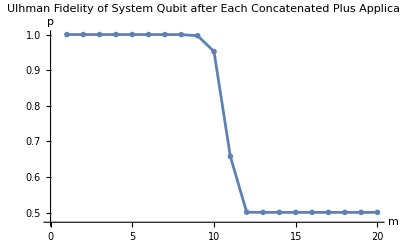
-Graphics-Concatenation LevelUlhman Fidelity

```mathematica
Labeled[ListPlot[fixedfidelities,
  Joined -> True,
  PlotMarkers -> Graphics@{Disk[{0, 0}, Scaled@0.02]},
  AxesLabel -> {"m", "p"},
  PlotLabel->"Ulhman Fidelity of System Qubit after Each Concatenated Plus Application"],  
  {"Concatenation Level", "Ulhman Fidelity"}, 
  {Bottom, Left}, RotateLabel -> True]
```